```mathematica
$Assumptions={h>0,R>0}
```

{h>0,R>0}

```mathematica
(* it works with both (ar+b) and (ar^-1+b) *)
```

```mathematica
(*Badri: use fixed R, not connect it to grid spacing*)
```

```mathematica
ssol=DSolve[{Laplacian[f[r],{r,θ,ϕ},"Spherical"]==0,f[h/2]==0},f[r],r]//Simplify
```

{{f[r]→(2/h-1/r) C[1]}}

```mathematica
f[r]/.ssol
```

{(h^2 (h-r))/(2 r)}

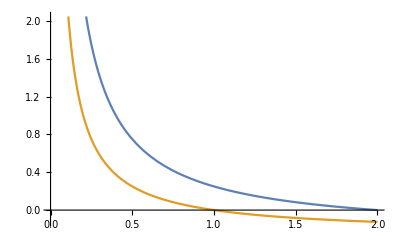

```mathematica
Plot[{-(1/h-1/r) C[1] /.C[1]->1/2/.h->2,-(1/h-1/r) C[1]/.C[1]->1/4/.h->1},{r,0,2}]
```

```mathematica
Solve[Integrate[-4π r^2(1/h-1/r) C[1],{r,0,h}]-Integrate[-4π r^2(2/h-1/r) C[2],{r,0,h/2}]==0,{C[1],C[2]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C[2]→4 C[1]}}

```mathematica
ρ[r_]:=-(1/h-1/r)a
QQQ=Integrate[4π r^2 ρ[r],{r,0,h}]
```

2/3 a h^2 π

```mathematica
sol=DSolve[{
Laplacian[Φ1[r],{r,θ,ϕ},"Spherical"]==-4π ρ[r],
Φ1[h]==Q/h, Φ1'[h]==-Q/h^2},Φ1[r],r]⟦1⟧//Simplify
```

{Φ1[r]→(3 h Q-2 a π (h-r)^3)/(3 h r)}

```mathematica
Φ1[r]/.sol/.Q->QQQ//Simplify
```

(2 a π (3 h^2-3 h r+r^2))/(3 h)

```mathematica
hh=0.5;QQ=1;
```

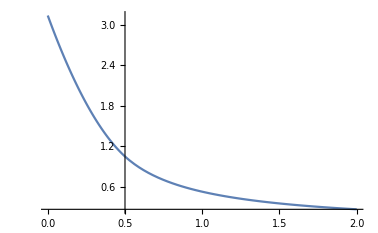

```mathematica
p1=Plot[Q/r/.Q->QQQ/.{h->hh,a->1,b->1,cc->1},{r,hh,4hh}];
p2=Plot[Φ1[r]/.sol/.Q->QQQ/.{h->hh,a->1,b->1,cc->1},{r,0,hh}];
Show[p1,p2,PlotRange->All]
```

```mathematica
coef[h_]:=1/h^3 Integrate[r^2 Φ1[r]/.sol/.Q->QQQ(*/.{a->h^3,b->h^2}*),{r,0,h}]//Simplify

(coef[h]-coef[h/2])/(coef[h/2]-coef[h/4])//FullSimplify
```

3/2

```mathematica
coef[h/2]
```

(9 a h π)/20

```mathematica
cl=1/h^3 Integrate[r^2(2 a π (3 h^2-3 h r+r^2))/(3 h),{r,0,h}]//Simplify
```

(3 a h π)/10

```mathematica
cm=1/(h/2)^3 Integrate[r^2(2 4a π (3 (h/2)^2-3 h/2 r+r^2))/(3 h/2),{r,0,h/2}]//Simplify
```

(3 a h π)/5

```mathematica
ch=1/(h/4)^3 Integrate[r^2(2 4 4a π (3 (h/4)^2-3 h/4 r+r^2))/(3 h/4),{r,0,h/4}]//Simplify
```

(6 a h π)/5

```mathematica
(cl-cm)/(cm-ch)
```

1/2